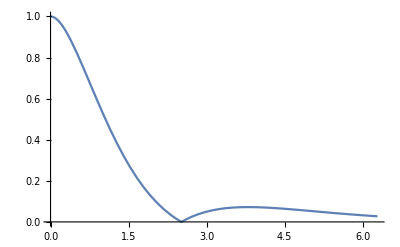

```mathematica
Plot[Abs[1+Δx-5/9(Δx)^2]Exp[-Δx],{Δx,0,2π},PlotRange->Full]
```

The intensity at the exit of a defocused three-blade NI is I=∫2|trr|^2(1+cos(ϕ+2πδy/Δ))dy where the integral is taken over the angular deviation parameter y=δθ/σ;

```mathematica
IO[x_]:=Integrate[(6 y^2+1)/(8(1+y^2)^3)(1+Cos[ 2π x y]),{y,-∞,∞}]  (*x=Δz/Subscript[Δ, H], that is the defocusing over the Pendellosung period*)
```

$Aborted

```mathematica
Integrate[(6 y^2+1)/(8(1+y^2)^3),{y,-∞,∞}]
```

(9 π)/64

The contrast function can be expressed as: with the average taken over uniformly distributed y

```mathematica
F1[x_]:=64/(9π)NIntegrate[(6 y^2+1)/(8(1+y^2)^3)Exp[I 2π x y],{y,-200,200}]
```

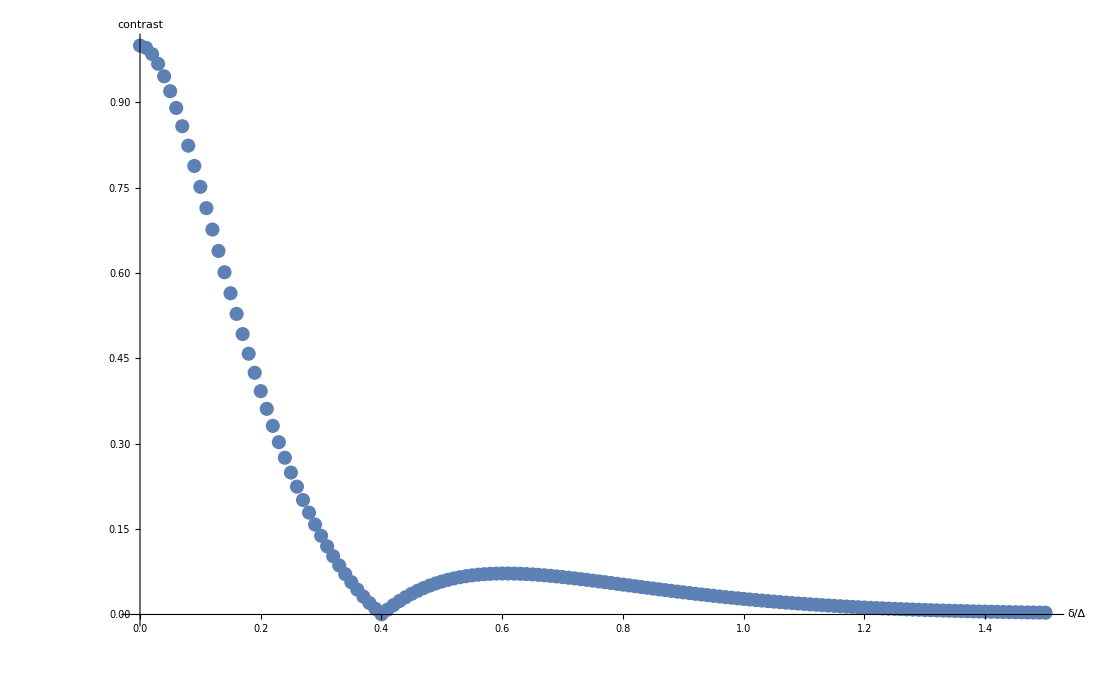

```mathematica
ListPlot[Table[{x,Abs[F1[x]]},{x,0,1.5,.01}],PlotRange->All, AxesLabel->{"δ/Δ","contrast"},AxesStyle->Directive[Black,20]]
```

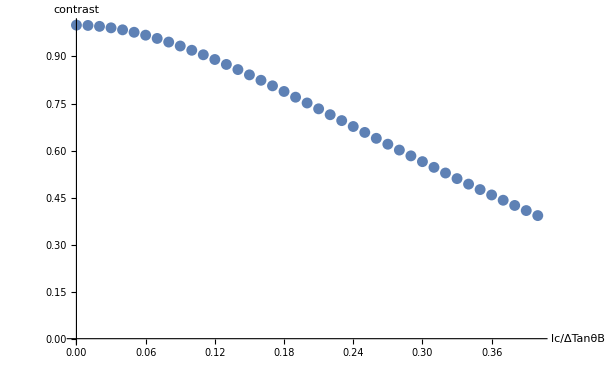

```mathematica
ListPlot[Table[{x,Abs[F1[x/2]]},{x,0,.4,.01}],PlotRange->All, AxesLabel->{"lc/ΔTanθB","contrast"},AxesStyle->Directive[Black,20]]
```

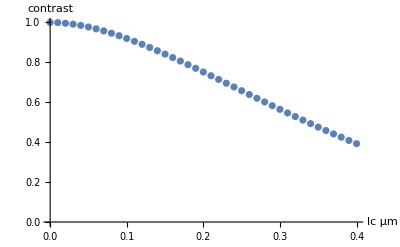

```mathematica
ListPlot[Table[{x,Abs[F1[x/2]]},{x,0,.4,.01}],PlotRange->All, AxesLabel->{"lc μm","contrast"},AxesStyle->Directive[Black,20]]
```

```mathematica
ListPlot[Table[{x,Abs[F1[x/2]]},{x,0,.4,.01}],PlotRange->All, AxesLabel->{"lc/ΔTanθB","contrast"},AxesStyle->Directive[Black,20]]
```

For 0.44 nm and Si [111] neutrons, Δ_H= 34.4 μm, and for 2.2 it is 90.4 μm. So for a contrast of 0.37, we have about δ/Δ=0.2

```mathematica
a=5.431*10^-10;
Tan[ArcSin[1.1*√3/(5.431)]]*90.4
```

33.8656

```mathematica
Tan[ArcSin[2.2*√3/(5.431)]]*34.4
```

33.8725

```mathematica
ArcSin[1.1/(√3*5.431)]
```

0.117205

```mathematica
ArcSin[2.71/(2 √3*5.431)]
```

0.144548

```mathematica
.1*34 
.2*34
.3*34
.4*34
```

3.4

6.8

10.2

13.6

```mathematica
Integrate[(6 y^2+1)/(8(1+y^2)^3)1/(√π y0)Exp[-y^2/y0^2],{y,-∞,∞}]
```

ConditionalExpression[((20+18 y0^2+ⅇ^(1/y0^2) √π √(1/y0^2) (-20-28 y0^2+9 y0^4))/(√(1/y0^2))-ⅇ^(1/y0^2) √π (-20-28 y0^2+9 y0^4) Erf[√(1/y0^2)])/(64 y0^5),Re[y0^2]>0]

ConditionalExpression[1/(64 √(1/y0^2) y0^5)(2 √π y0 (10+9 y0^2)+ⅇ^(1/y0^2) π √(1/y0^2) y0 (-20-28 y0^2+9 y0^4)-ⅇ^(1/y0^2) π (-20-28 y0^2+9 y0^4) Erf[1/y0]),Re[y0^2]>0]

```mathematica
FullSimplify[1/(64 y0^5)((20+18 y0^2+ⅇ^(1/y0^2) √π √(1/y0^2) (-20-28 y0^2+9 y0^4))/(√(1/y0^2))-ⅇ^(1/y0^2) √π (-20-28 y0^2+9 y0^4) Erf[√(1/y0^2)]),y0>0]
```

(2 y0 (10+9 y0^2)+ⅇ^(1/y0^2) √π (-20-28 y0^2+9 y0^4) Erfc[1/y0])/(64 y0^5)

```mathematica
Integrate[1/(√π y0)Exp[-y^2/y0^2],{y,-∞,∞}]
```

ConditionalExpression[1/(√(1/y0^2) y0),Re[y0^2]>0]

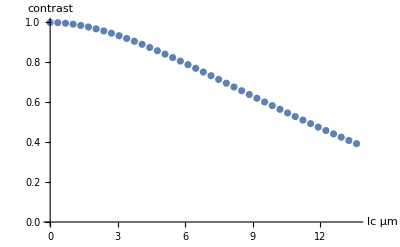

```mathematica
ListPlot[Table[{x*34,Abs[F1[x/2]]},{x,0,.4,.01}],PlotRange->All, AxesLabel->{"lc μm","contrast"},AxesStyle->Directive[Black,20]]
```

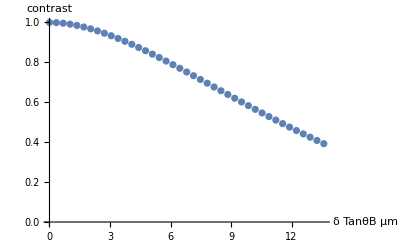

```mathematica
ListPlot[Table[{x*34,Abs[F1[x/2]]},{x,0,.4,.01}],PlotRange->All, AxesLabel->{"δ TanθB μm","contrast"},AxesStyle->Directive[Black,20]]
```

```mathematica
1/Exp[1.0]
```

0.367879

```mathematica
Series[Exp[I 2π x y],{x,0,3}]
```

1+2 ⅈ π y x-2 (π^2 y^2) x^2-4/3 ⅈ π^3 y^3 x^3+O[x]^4

```mathematica
64/(9π)Integrate[(6 y^2+1)/(8(1+y^2)^3)(1+ⅈ π y x-1/2 (π^2 y^2) x^2),{y,-∞,∞}]
```

1/18 (18-19 π^2 x^2)

```mathematica
F2[x_]=64/(9π)Integrate[(6 y^2+1)/(8(1+y^2)^3)(1+2 ⅈ π y x-2 (π^2 y^2) x^2),{y,-∞,∞}]
```

1/9 (9-38 π^2 x^2)

```mathematica
38/9
```

38/9

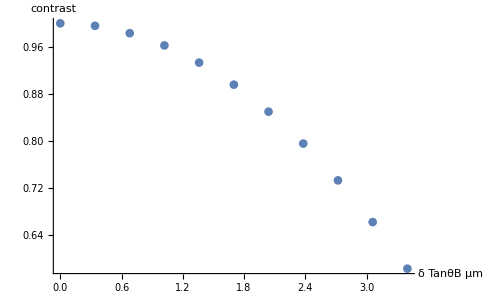

```mathematica
ListPlot[Table[{x*34,Abs[F2[x]]},{x,0,.1,.01}],PlotRange->All, AxesLabel->{"δ TanθB μm","contrast"},AxesStyle->Directive[Black,20]]
```

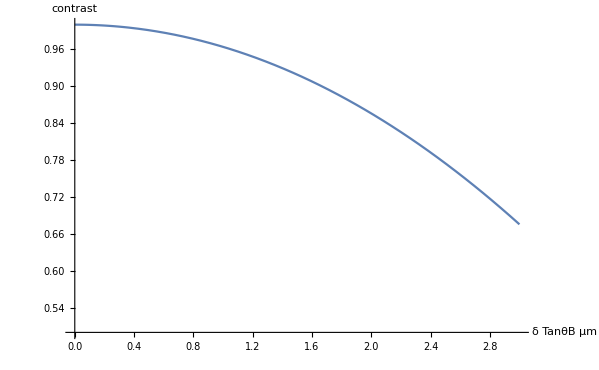

```mathematica
Plot[Abs[F2[x/34]],{x,0,3},PlotRange->{.5,1}, AxesLabel->{"δ TanθB μm","contrast"},AxesStyle->Directive[Black,20]]
```

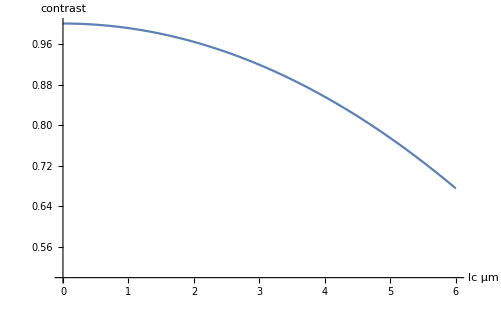

```mathematica
Plot[Abs[F2[x/68]],{x,0,6},PlotRange->{.5,1}, AxesLabel->{"lc μm","contrast"},AxesStyle->Directive[Black,20]]
```

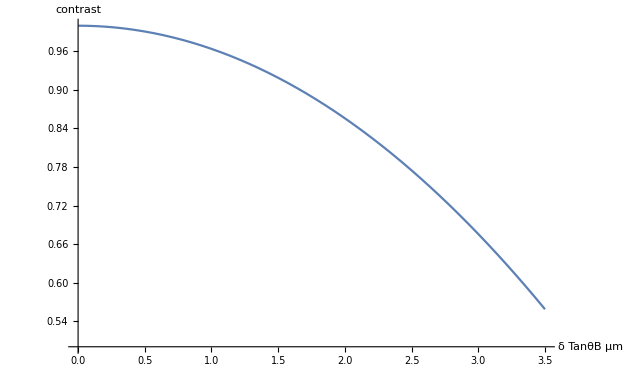

```mathematica
Plot[Abs[F2[x/34]],{x,0,3.5},PlotRange->{.5,1}, AxesLabel->{"δ TanθB μm","contrast"},AxesStyle->Directive[Black,20]]
```

```mathematica
F2[x/34]
```

1/9 (9-(19 π^2 x^2)/578)

```mathematica
F3[x_,a1_]:=128/(9π)NIntegrate[((Sin[a1 √(1+y^2)]^2)/(1+y^2))^2(1-(Sin[a1 √(1+y^2)]^2)/(1+y^2))(Exp[I 2π x y]),{y,-200,200}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

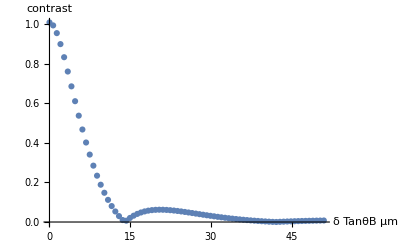

```mathematica
ListPlot[Table[{x*34,Abs[F3[x,74]]},{x,0,1.5,.02}],PlotRange->All, AxesLabel->{"δ TanθB μm","contrast"},AxesStyle->Directive[Black,20]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

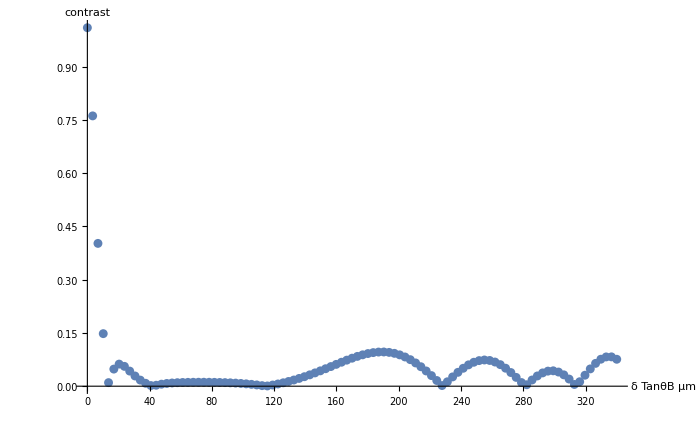

```mathematica
ListPlot[Table[{x*34,Abs[F3[x,74]]},{x,0,10,.1}],PlotRange->All, AxesLabel->{"δ TanθB μm","contrast"},AxesStyle->Directive[Black,20]]
```

```mathematica
ArcCos[0.85]
```

```mathematica
0.5548110329800715/3.14
```

0.176691

```mathematica
2048/128
```

16

```mathematica
Pi/75.0
```

0.0418879

```mathematica
Pi/73.
```

0.0430355

```mathematica
Pi/0.04305
```

72.9754